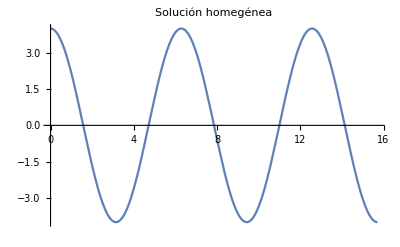

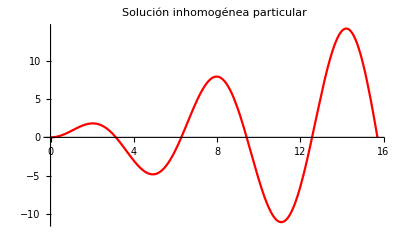

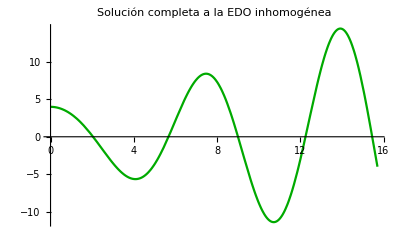

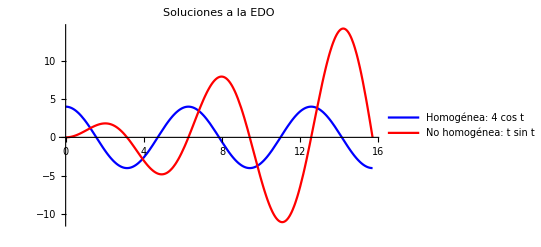

```mathematica
Plot[4 Cos [x], {x,0, 5 Pi}, PlotLabel->"Solución homegénea "]
Plot[x Sin [x], {x, 0, 5 Pi}, PlotLabel->"Solución inhomogénea particular", PlotStyle->Red]
Plot[4 Cos[x] + x Sin [x],{x,0,5 Pi}, PlotLabel->Style["Solución completa a la EDO inhomogénea", Black, FontSize->14], PlotStyle->Darker[Green]]
Plot[{4 Cos[x], x Sin[x]},{x,0, 5 Pi}, PlotLegends->{"Homogénea: 4 cos t", "No homogénea: t sin t"}, PlotLabel->Style["Soluciones a la EDO", Black, FontSize->14], PlotStyle->{Blue, Red}]
```